```mathematica
<<PlotLegends`
Integrate[mu*E^(e/T)/((E^(e/T)+1)^2*T)*e^2,{e,0,Infinity}]
```

ConditionalExpression[1/6 mu π^2 T^2,Re[T]>0]

```mathematica
Integrate[mu*E^(e/T)/((E^(e/T)-1)^2*T)*e^2,{e,0,Infinity}]
```

ConditionalExpression[1/3 mu π^2 T^2,Re[T]>0]

```mathematica
Series[1/(E^((e-mu)/T)+1),{mu,0,1}]
```

1/(1+ⅇ^(e/T))+(ⅇ^(e/T) mu)/((1+ⅇ^(e/T))^2 T)+O[mu]^2

```mathematica
Integrate[ⅇ^(e/T)/((-1+ⅇ^(e/T))^2)*e^2,{e,0,Infinity}]
```

ConditionalExpression[(π^2 T^3)/3,Re[T]>0]

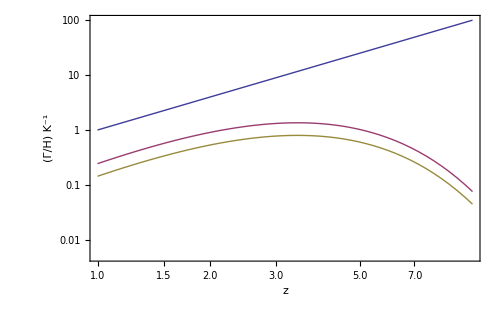

```mathematica
LogLogPlot[{z^2,3/Pi^2*(1+1/3)z^4*BesselK[1,z],3/Pi^2*(344/537+26/179)z^4*BesselK[1,z]},{z,1,10},PlotRange-> {0.005,100},PlotLegend -> {Subscript[Γ,N],"T>>"Superscript[10,13]},LegendPosition -> {1,-.3},ImageSize->500,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"(Γ/H)"Superscript["K",-1],None},{"z",None}},FrameTicks->All]
```